```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
gpdg=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpdg;
Her=Query[1,2]@gpdg;
Hda=Query[1,3]@gpdg;
Edg=Query[2,1]@gpdg;
Eer=Query[2,2]@gpdg;
Eda=Query[2,3]@gpdg;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t];
```

```mathematica
(*Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];*)
```

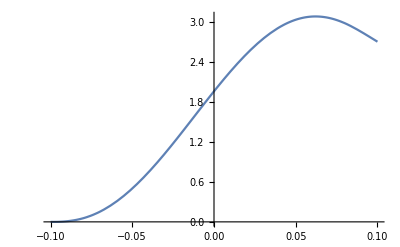

```mathematica
Plot[I*Herf[x,-1],{x,-0.1,0.1}]
```

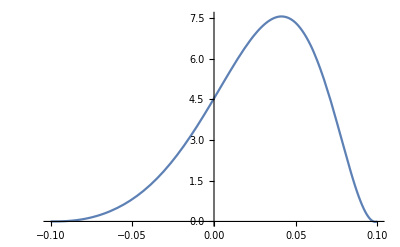

```mathematica
Plot[I*Hdaf[x,-1],{x,-0.1,0.1}]
```

```mathematica
Plot[I*Herf[x,-1],{x,-0.1,0.1}]
```

-Graphics-

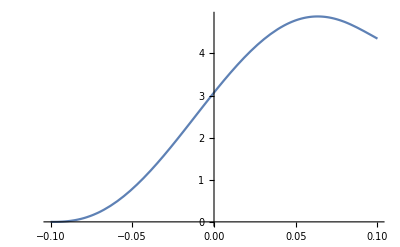

```mathematica
Plot[I*Eerf[x,-1],{x,-0.1,0.1}]
```

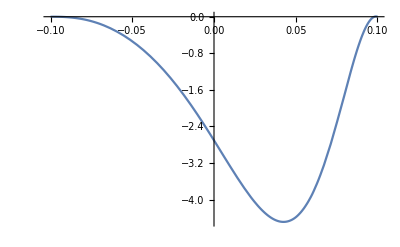

```mathematica
Plot[I*Edaf[x,-1],{x,-0.1,0.1}]
```

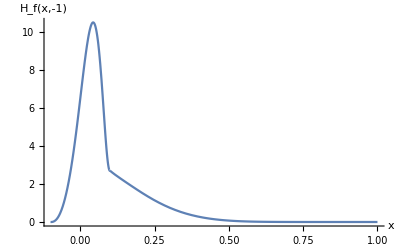

```mathematica
pHf2d=Show[Plot[I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_f(x,-1)"}]
```

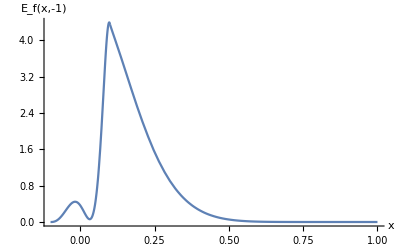

```mathematica
pEf2d=Show[Plot[I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_f(x,-1)"}]
```

```mathematica
Plot3D[-I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-

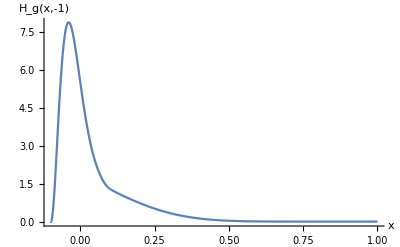

```mathematica
pHg2d=Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_g(x,-1)"}]
```

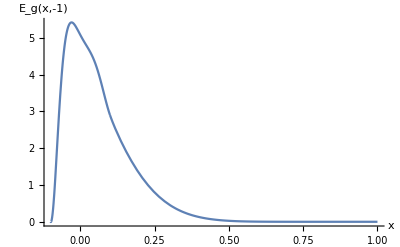

```mathematica
pEg2d=Show[Plot[-I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_g(x,-1)"}]
```

```mathematica
pHg3d=Show[Plot3D[-I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_g(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEg3d=Show[Plot3D[-I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_g(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pHf3d=Show[Plot3D[I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_f(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEf3d=Show[Plot3D[I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_f(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
fpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Hu-0.1.pdf"}];
```

```mathematica
fpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Eu-0.1.pdf"}];
```

```mathematica
fpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Eu-0.1-2d.pdf"}];
```

```mathematica
fpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"f-Hu-0.1-2d.pdf"}];
```

```mathematica
gpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Hu-0.1.pdf"}];
gpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Hu-0.1-2d.pdf"}];
```

```mathematica
gpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Eu-0.1.pdf"}];
gpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"g-Eu-0.1-2d.pdf"}];
```

```mathematica
Export[gpathH3d,pHg3d]
Export[gpathH,pHg2d]
```

G:\calc-online\gpd\3dre\228test\g-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\g-Hu-0.1-2d.pdf

```mathematica
Export[gpathE3d,pEg3d]
Export[gpathE,pEg2d]
```

G:\calc-online\gpd\3dre\228test\g-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\g-Eu-0.1-2d.pdf

```mathematica
Export[fpathH3d,pHf3d]
Export[fpathH,pHf2d]
```

G:\calc-online\gpd\3dre\228test\f-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\f-Hu-0.1-2d.pdf

```mathematica
Export[fpathE3d,pEf3d]
Export[fpathE,pEf2d]
```

G:\calc-online\gpd\3dre\228test\f-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\f-Eu-0.1-2d.pdf

```mathematica
SubscriptBox["H",e]//DisplayForm
```

H_e

```mathematica
Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

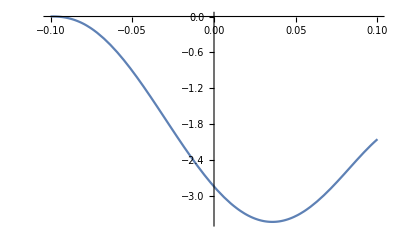

```mathematica
Plot[-I*Chop[Eerf[x,-0.1],10^-9],{x,-0.1,0.1}]
```

```mathematica
Eerf[0,-0.1]
```

0.-2.83547 ⅈ

```mathematica
Eerf[0.02,-0.1]
```

-8.32662×10^-26-3.30567 ⅈ

```mathematica
Eerf[-0.005,-0.1]
```

-1.49999×10^-11-2.67216 ⅈ

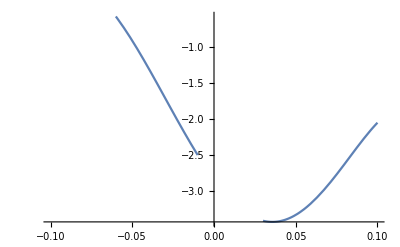

```mathematica
Plot[-I*Eerf[x,-0.1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-